Below is the Mathematica code used for calculating values for the measurements PDF f_Y(y), using said values to calculate approximate expectation values for bin counts {ν_i}, using true PDF f_X(x) to calculate exact expectation values for bin counts {μ_j}, and exporting data to CSV files for use in R code.

Defined below are:
	• Each true PDF f_X(x), f1[x] and f2[x].
	• The Kernel g(x,y), g[x,y].
	• The efficiency ϵ(x), ϵ[x].

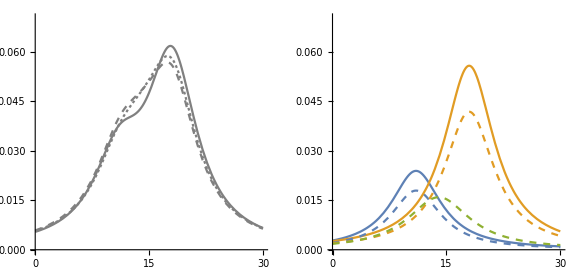

```mathematica
loc={11,18,14};
scale={4,4,5};
p=0.25;
p1 = {0.3,0.7};p2={(1-p)p1[[1]],(1-p)p1[[2]],p};
fp1[x_]:=PDF[CauchyDistribution[loc[[1]],scale[[1]]],x];
fp2[x_]:=PDF[CauchyDistribution[loc[[2]],scale[[2]]],x];
fp3[x_]:=PDF[CauchyDistribution[loc[[3]],scale[[3]]],x];
f1[x_]:= p1[[1]] fp1[x]+p1[[2]]fp2[x];
f2[x_]:=p2[[1]] fp1[x]+p2[[2]]fp2[x]+p2[[3]] fp3[x];
g[x_,y_]:=PDF[NormalDistribution[-x^(1/4),Log[(x+10)/4]],y-x];
ϵ[x_]:=1-Exp[-√x/4];
GraphicsGrid[{{Plot[{f1[x],f2[x],(p2[[1]]-0.04) fp1[x]+(p2[[2]]+0.03)fp2[x]+(p2[[3]]+0.01) fp3[x]},{x,0,30},PlotStyle->{Gray,{Dashed,Gray},{Dashing[Tiny],Gray}},
PlotRange->{{0,30},{0,0.07}},ImageSize->{250,250}],
Show[Plot[{p1[[1]] fp1[x],p1[[2]]fp2[x]},{x,0,30},
PlotRange->{{0,30},{0,0.07}},ImageSize->{250,250}],
Plot[{p2[[1]] fp1[x],p2[[2]]fp2[x],p2[[3]] fp3[x]},{x,0,30},PlotStyle->{Dashed},
PlotRange->{{0,30},{0,0.07}},ImageSize->{250,250}]]}},ImageSize->Large]
```

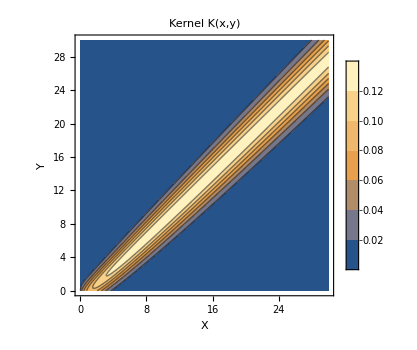

```mathematica
ContourPlot[ϵ[x]g[x,y],{x,0,30},{y,0,30},PlotRange->All,PlotLegends->Automatic,
PlotPoints->50,MaxRecursion->3,ImageSize->{350,350},
PlotLabel->"Kernel K(x,y)",FrameLabel->{"X","Y"}]
```

Performed below:
	• The sequence of values for x and y from 0 to 30 with step sizes of 0.01 are generated for plotting, xys.
	• The values of each true PDF f_x(x) are calculated for plotting, f1xs and f2xs. 
	• Each PDF f_x(x) is integrated across bins of width Δx=1 to produce its corresponding histogram, hist1xs and hist2xs.

```mathematica
xys =Table[N[x/100],{x,0,3000}];
f1xs = N[f1[xys]];
f2xs = N[f2[xys]];
hist1xs = N[Table[∫_(i-1)^i f1[x]ⅆx,{i,1,30}]];
hist2xs = N[Table[∫_(i-1)^i f2[x]ⅆx,{i,1,30}]];
```

Performed below:
	• Point-by-point calculations of ∫_(-∞)^∞ f_X(x)ϵ(x)g(x,y)ⅆx to get values for each f_Y(y) for each bin separately, f1ysd[[i]] and f2ysd[[i]].
	• The mean for each bin is then found get hist1ys and hist2ys. 
	• The bins are combined into the values of each f_y(y) to be plotted, f1ys and f2ys.
The first item takes several minutes to perform.

```mathematica
f1ysd = Table[Null,{x,1,30}];
For[i=1,i<31,i++,
f1ysd[[i]] = NIntegrate[ExpandAll[f1[x]ϵ[x]g[x,N[Table[y/100,{y,(i-1)*100,i*100}]]]],{x,0,30}]];
f2ysd = Table[Null,{x,1,30}];
For[i=1,i<31,i++,
f2ysd[[i]] = NIntegrate[ExpandAll[f2[x]ϵ[x]g[x,N[Table[y/100,{y,(i-1)*100,i*100}]]]],{x,0,30}]];
```

```mathematica
hist1ys =Table[Mean[f1ysd[[i]]],{i,1,30}];
hist2ys =Table[Mean[f2ysd[[i]]],{i,1,30}];
seq =Table[x,{x,2,101}];
f1ys = Flatten[Join[{f1ysd[[1]]},Table[f1ysd[[i]][[seq]],{i,2,30}]]];
f2ys = Flatten[Join[{f2ysd[[1]]},Table[f2ysd[[i]][[seq]],{i,2,30}]]];
```

Plotting f1xs, f1ys, f2xs, f2ys, hist1xs, hist1ys, hist2xs, and hist2ys

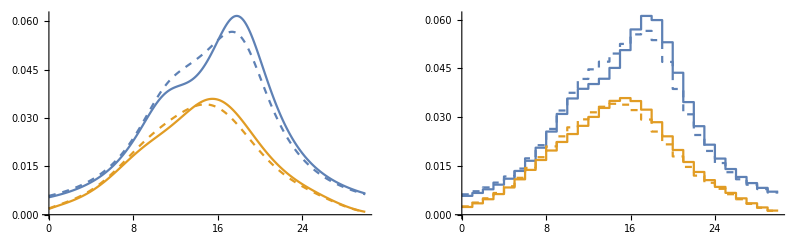

```mathematica
xys1=xys;xys2=xys;
GraphicsGrid[{{Show[ListLinePlot[{Transpose[{xys1,f1xs}],Transpose[{xys1,f1ys}]}],ListLinePlot[{Transpose[{xys2,f2xs}],Transpose[{xys2,f2ys}]},PlotStyle->Dashed]],
Show[ListStepPlot[{Transpose[{Table[x,{x,0,29}],hist1xs}],Transpose[{Table[x,{x,0,29}],hist1ys}]}],
ListStepPlot[{Transpose[{Table[x,{x,0,29}],hist2xs}],Transpose[{Table[x,{x,0,29}],hist2ys}]},PlotStyle->Dashed]]}}]
```

Saving f_Y(y) estimates.

```mathematica
SetDirectory[NotebookDirectory[]];
Export["f1yEstimate.csv",
Transpose[{PrependTo[xys1,Y],PrependTo[f1ys,Density]}]];
Export["f2yEstimate.csv",
Transpose[{PrependTo[xys2,Y],PrependTo[f2ys,Density]}]];
```

Generating column contents for the tibble exp_hist to be used for plotting histxs and histxy in R.

```mathematica
lbin1 = Join[Table[x,{x,0,29}],Table[x,{x,0,29}]];
bin1 = Join[Table[x,{x,1,30}],Table[x,{x,1,30}]];
treat1 = Join[Table["Truth",{x,1,30}],Table["Measured",{x,1,30}]];
lcount1 = Join[{0},hist1xs[[Table[x,{x,1,29}]]],
{0},hist1ys[[Table[x,{x,1,29}]]]];
count1 = Join[hist1xs,hist1ys];
lbin2 = Join[Table[x,{x,0,29}],Table[x,{x,0,29}]];
bin2 = Join[Table[x,{x,1,30}],Table[x,{x,1,30}]];
treat2 = Join[Table["Truth",{x,1,30}],Table["Measured",{x,1,30}]];
lcount2 = Join[{0},hist2xs[[Table[x,{x,1,29}]]],
{0},hist2ys[[Table[x,{x,1,29}]]]];
count2 = Join[hist2xs,hist2ys];
```

Saving expected value histogram data.

```mathematica
Export["hist1Expected.csv",
Transpose[{PrependTo[lbin1,LBin],PrependTo[bin1,Bin],
PrependTo[lcount1,LCounts],PrependTo[count1,Counts],
PrependTo[treat1,Treatment]}]];
Export["hist2Expected.csv",
Transpose[{PrependTo[lbin2,LBin],PrependTo[bin2,Bin],
PrependTo[lcount2,LCounts],PrependTo[count2,Counts],
PrependTo[treat2,Treatment]}]];
```